```mathematica
SetDirectory[NotebookDirectory[]]
```

```mathematica
<<TMToCWTM`
```

```mathematica
<<ColoredToBinCWTM`
```

```mathematica
<<CWTMToTag`
```

```mathematica
<<TagToCT`
```

```mathematica
tMToCT[rule:{({_, _} -> {_, _, _})...}]:=Tag1ToCT[{2,CWTMToTag[ColoredToBinCWTM[TMToCWTM[rule]]]}]
```

```mathematica
tMToCTInit[init:{s_, as_List},rule:{({_, _} -> {_, _, _})...}]:=Tag1ToCTInit[CWTMToTagInit[ColoredToBinCWTMInit[TMToCWTMInit[init],#]],CWTMToTag[ColoredToBinCWTM[#]]]&[TMToCWTM[rule]]
```

```mathematica
tM=TuringMachine[{596440,2,3}];
```

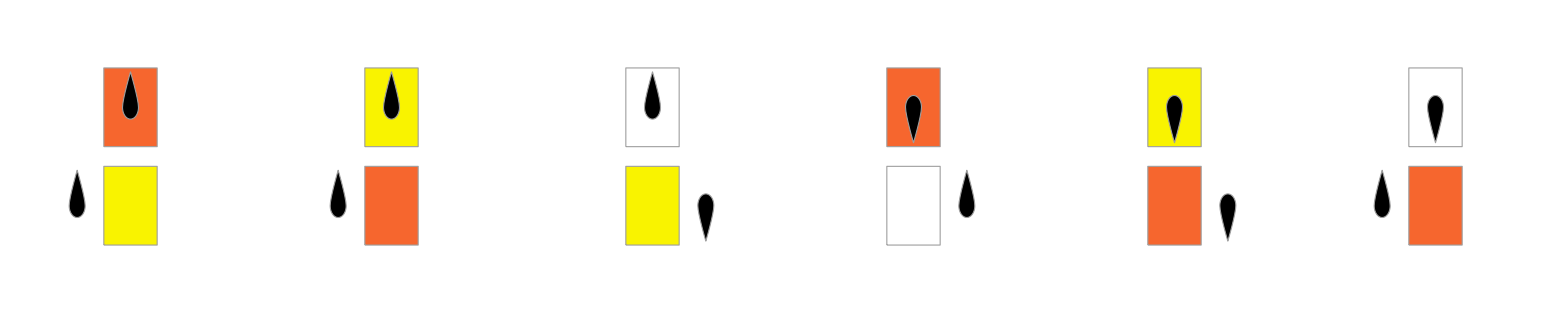

```mathematica
RulePlot[tM]
```

```mathematica
tMRule=ResourceFunction["ComputationalSystemRules"][tM]
```

{{1,2}→{1,1,-1},{1,1}→{1,2,-1},{1,0}→{2,1,1},{2,2}→{1,0,1},{2,1}→{2,2,1},{2,0}→{1,2,-1}}

```mathematica
cWTMRule=TMToCWTM[tMRule]
```

{{1,2}→{Fl[1,1],{Ml}},{1,1}→{Fl[1,2],{Ml}},{1,0}→{2,{1}},{1,L}→{2,{L,1}},{1,R}→{Fr[1],{Ml,R}},{2,2}→{1,{0}},{2,1}→{2,{2}},{2,0}→{Fl[1,2],{Ml}},{2,R}→{Fl[1,R],{Ml,2}},{2,L}→{Fl[1,2],{L,Ml}},{Fl[1,2],2}→{Fl[1,2],{2}},{Fl[1,2],1}→{Fl[1,1],{2}},{Fl[1,2],0}→{Fl[1,0],{2}},{Fl[1,2],L}→{Fl[1,L],{2}},{Fl[1,2],R}→{Fl[1,R],{2}},{Fl[1,2],Ml}→{Fl[1,1],{Ml}},{Fr[1],2}→{Fr[1],{2}},{Fr[1],Ml}→{2,{1}},{Fl[1,1],2}→{Fl[1,2],{1}},{Fl[1,1],1}→{Fl[1,1],{1}},{Fl[1,1],0}→{Fl[1,0],{1}},{Fl[1,1],L}→{Fl[1,L],{1}},{Fl[1,1],R}→{Fl[1,R],{1}},{Fl[1,1],Ml}→{Fl[1,2],{Ml}},{Fr[1],1}→{Fr[1],{1}},{Fr[1],Ml}→{2,{1}},{Fl[1,0],2}→{Fl[1,2],{0}},{Fl[1,0],1}→{Fl[1,1],{0}},{Fl[1,0],0}→{Fl[1,0],{0}},{Fl[1,0],L}→{Fl[1,L],{0}},{Fl[1,0],R}→{Fl[1,R],{0}},{Fl[1,0],Ml}→{2,{1}},{Fr[1],0}→{Fr[1],{0}},{Fr[1],Ml}→{2,{1}},{Fl[1,L],2}→{Fl[1,2],{L}},{Fl[1,L],1}→{Fl[1,1],{L}},{Fl[1,L],0}→{Fl[1,0],{L}},{Fl[1,L],L}→{Fl[1,L],{L}},{Fl[1,L],R}→{Fl[1,R],{L}},{Fl[1,L],Ml}→{2,{L,1}},{Fr[1],L}→{Fr[1],{L}},{Fr[1],Ml}→{2,{1}},{Fl[1,R],2}→{Fl[1,2],{R}},{Fl[1,R],1}→{Fl[1,1],{R}},{Fl[1,R],0}→{Fl[1,0],{R}},{Fl[1,R],L}→{Fl[1,L],{R}},{Fl[1,R],R}→{Fl[1,R],{R}},{Fl[1,R],Ml}→{Fr[1],{Ml,R}},{Fr[1],R}→{Fr[1],{R}},{Fr[1],Ml}→{2,{1}},{Fl[2,2],2}→{Fl[2,2],{2}},{Fl[2,2],1}→{Fl[2,1],{2}},{Fl[2,2],0}→{Fl[2,0],{2}},{Fl[2,2],L}→{Fl[2,L],{2}},{Fl[2,2],R}→{Fl[2,R],{2}},{Fl[2,2],Ml}→{1,{0}},{Fr[2],2}→{Fr[2],{2}},{Fr[2],Ml}→{Fl[1,2],{Ml}},{Fl[2,1],2}→{Fl[2,2],{1}},{Fl[2,1],1}→{Fl[2,1],{1}},{Fl[2,1],0}→{Fl[2,0],{1}},{Fl[2,1],L}→{Fl[2,L],{1}},{Fl[2,1],R}→{Fl[2,R],{1}},{Fl[2,1],Ml}→{2,{2}},{Fr[2],1}→{Fr[2],{1}},{Fr[2],Ml}→{Fl[1,2],{Ml}},{Fl[2,0],2}→{Fl[2,2],{0}},{Fl[2,0],1}→{Fl[2,1],{0}},{Fl[2,0],0}→{Fl[2,0],{0}},{Fl[2,0],L}→{Fl[2,L],{0}},{Fl[2,0],R}→{Fl[2,R],{0}},{Fl[2,0],Ml}→{Fl[1,2],{Ml}},{Fr[2],0}→{Fr[2],{0}},{Fr[2],Ml}→{Fl[1,2],{Ml}},{Fl[2,R],2}→{Fl[2,2],{R}},{Fl[2,R],1}→{Fl[2,1],{R}},{Fl[2,R],0}→{Fl[2,0],{R}},{Fl[2,R],L}→{Fl[2,L],{R}},{Fl[2,R],R}→{Fl[2,R],{R}},{Fl[2,R],Ml}→{Fl[1,R],{Ml,2}},{Fr[2],R}→{Fr[2],{R}},{Fr[2],Ml}→{Fl[1,2],{Ml}},{Fl[2,L],2}→{Fl[2,2],{L}},{Fl[2,L],1}→{Fl[2,1],{L}},{Fl[2,L],0}→{Fl[2,0],{L}},{Fl[2,L],L}→{Fl[2,L],{L}},{Fl[2,L],R}→{Fl[2,R],{L}},{Fl[2,L],Ml}→{Fl[1,2],{L,Ml}},{Fr[2],L}→{Fr[2],{L}},{Fr[2],Ml}→{Fl[1,2],{Ml}}}

```mathematica
cWTMInit=TMToCWTMInit[{1,{0}}]
```

{1,{0,R,L}}

```mathematica
binCWTMRule=ColoredToBinCWTM[cWTMRule];
```

```mathematica
Length[binCWTMRule]
```

455

```mathematica
binCWTMRule[[;;20]]//Column
```

{Li[1,{{0}},{0,1}],0}→{Li[Fl[1,1],{{0},{1},{1}},{}],{0}}
{Li[Fl[1,1],{{0},{1},{1}},{}],0}→{Li[Fl[1,1],{{1},{1}},{0}],{0}}
{Li[Fl[1,1],{{0},{1},{1}},{}],1}→{Li[Fl[1,1],{{1},{1}},{1}],{0}}
{Li[Fl[1,1],{{1},{1}},{0}],0}→{Li[Fl[1,1],{{1}},{0,0}],{1}}
{Li[Fl[1,1],{{1},{1}},{0}],1}→{Li[Fl[1,1],{{1}},{0,1}],{1}}
{Li[Fl[1,1],{{1},{1}},{1}],0}→{Li[Fl[1,1],{{1}},{1,0}],{1}}
{Li[1,{{0}},{0,0}],1}→{Li[Fl[1,2],{{0},{1},{1}},{}],{0}}
{Li[Fl[1,2],{{0},{1},{1}},{}],0}→{Li[Fl[1,2],{{1},{1}},{0}],{0}}
{Li[Fl[1,2],{{0},{1},{1}},{}],1}→{Li[Fl[1,2],{{1},{1}},{1}],{0}}
{Li[Fl[1,2],{{1},{1}},{0}],0}→{Li[Fl[1,2],{{1}},{0,0}],{1}}
{Li[Fl[1,2],{{1},{1}},{0}],1}→{Li[Fl[1,2],{{1}},{0,1}],{1}}
{Li[Fl[1,2],{{1},{1}},{1}],0}→{Li[Fl[1,2],{{1}},{1,0}],{1}}
{Li[1,{{0}},{0,0}],0}→{Li[2,{{0},{0},{1}},{}],{0}}
{Li[2,{{0},{0},{1}},{}],0}→{Li[2,{{0},{1}},{0}],{0}}
{Li[2,{{0},{0},{1}},{}],1}→{Li[2,{{0},{1}},{1}],{0}}
{Li[2,{{0},{1}},{0}],0}→{Li[2,{{1}},{0,0}],{0}}
{Li[2,{{0},{1}},{0}],1}→{Li[2,{{1}},{0,1}],{0}}
{Li[2,{{0},{1}},{1}],0}→{Li[2,{{1}},{1,0}],{0}}
{Li[1,{{0}},{1,0}],0}→{Li[2,{{1,0},{0,0},{0,1}},{}],{0}}
{Li[2,{{1,0},{0,0},{0,1}},{}],0}→{Li[2,{{0,0},{0,1}},{0}],{1,0}}

```mathematica
binCWTMInit=ColoredToBinCWTMInit[cWTMInit,cWTMRule]
```

{Li[2,{{1}},{1,0}],{1,1,0,0,0,0}}

```mathematica
tagRule=CWTMToTag[binCWTMRule];
```

```mathematica
Length[tagRule]
```

16584

```mathematica
tagRule[[;;25]]//Column
```

0→{}
H_(1,Li[1,{{0}},{0,0}])→{H_(2,Li[1,{{0}},{0,0}]),h_(2,Li[1,{{0}},{0,0}])}
A_(1,Li[1,{{0}},{0,0}])→{A_(2,Li[1,{{0}},{0,0}]),A_(2,Li[1,{{0}},{0,0}])}
a_(1,Li[1,{{0}},{0,0}])→{C_(2,Li[1,{{0}},{0,0}]),C_(2,Li[1,{{0}},{0,0}])}
B_(1,Li[1,{{0}},{0,0}])→{B_(2,Li[1,{{0}},{0,0}]),B_(2,Li[1,{{0}},{0,0}])}
b_(1,Li[1,{{0}},{0,0}])→{D_(2,Li[1,{{0}},{0,0}]),D_(2,Li[1,{{0}},{0,0}])}
C_(1,Li[1,{{0}},{0,0}])→{C_(2,Li[1,{{0}},{0,0}]),C_(2,Li[1,{{0}},{0,0}])}
D_(1,Li[1,{{0}},{0,0}])→{D_(2,Li[1,{{0}},{0,0}]),D_(2,Li[1,{{0}},{0,0}])}
U_(1,Li[1,{{0}},{0,0}])→{U_(2,Li[1,{{0}},{0,0}]),u_(2,Li[1,{{0}},{0,0}])}
V_(1,Li[1,{{0}},{0,0}])→{V_(2,Li[1,{{0}},{0,0}]),V_(2,Li[1,{{0}},{0,0}])}
X_(1,Li[1,{{0}},{0,0}])→{X_(2,Li[1,{{0}},{0,0}]),x_(2,Li[1,{{0}},{0,0}])}
Y_(1,Li[1,{{0}},{0,0}])→{Y_(2,Li[1,{{0}},{0,0}]),Y_(2,Li[1,{{0}},{0,0}])}
H_(2,Li[1,{{0}},{0,0}])→{H_(3,Li[1,{{0}},{0,0}]),$}
h_(2,Li[1,{{0}},{0,0}])→{$,H_(3,Li[1,{{0}},{0,0}]),$}
A_(2,Li[1,{{0}},{0,0}])→{A_(3,Li[1,{{0}},{0,0}]),A_(3,Li[1,{{0}},{0,0}])}
B_(2,Li[1,{{0}},{0,0}])→{B_(3,Li[1,{{0}},{0,0}]),B_(3,Li[1,{{0}},{0,0}])}
C_(2,Li[1,{{0}},{0,0}])→{C_(3,Li[1,{{0}},{0,0}]),C_(3,Li[1,{{0}},{0,0}])}
D_(2,Li[1,{{0}},{0,0}])→{D_(3,Li[1,{{0}},{0,0}]),D_(3,Li[1,{{0}},{0,0}])}
U_(2,Li[1,{{0}},{0,0}])→{U_(3,Li[1,{{0}},{0,0}])}
u_(2,Li[1,{{0}},{0,0}])→{V_(3,Li[1,{{0}},{0,0}])}
X_(2,Li[1,{{0}},{0,0}])→{X_(3,Li[1,{{0}},{0,0}]),X_(3,Li[1,{{0}},{0,0}])}
x_(2,Li[1,{{0}},{0,0}])→{Y_(3,Li[1,{{0}},{0,0}]),Y_(3,Li[1,{{0}},{0,0}])}
V_(2,Li[1,{{0}},{0,0}])→{V_(3,Li[1,{{0}},{0,0}])}
Y_(2,Li[1,{{0}},{0,0}])→{Y_(3,Li[1,{{0}},{0,0}]),Y_(3,Li[1,{{0}},{0,0}])}
H_(3,Li[1,{{0}},{0,0}])→{H_(4,Li[1,{{0}},{0,0}]),h_(4,Li[1,{{0}},{0,0}])}

```mathematica
tagInit=CWTMToTagInit[binCWTMInit]
```

{H_(2,Li[2,{{1}},{1,0}]),h_(2,Li[2,{{1}},{1,0}]),B_(2,Li[2,{{1}},{1,0}]),B_(2,Li[2,{{1}},{1,0}]),U_(2,Li[2,{{1}},{1,0}]),u_(2,Li[2,{{1}},{1,0}]),U_(2,Li[2,{{1}},{1,0}]),u_(2,Li[2,{{1}},{1,0}]),U_(2,Li[2,{{1}},{1,0}]),u_(2,Li[2,{{1}},{1,0}]),U_(2,Li[2,{{1}},{1,0}]),u_(2,Li[2,{{1}},{1,0}]),U_(2,Li[2,{{1}},{1,0}]),u_(2,Li[2,{{1}},{1,0}]),U_(2,Li[2,{{1}},{1,0}]),u_(2,Li[2,{{1}},{1,0}]),U_(2,Li[2,{{1}},{1,0}]),u_(2,Li[2,{{1}},{1,0}]),U_(2,Li[2,{{1}},{1,0}]),u_(2,Li[2,{{1}},{1,0}]),B_(2,Li[2,{{1}},{1,0}]),B_(2,Li[2,{{1}},{1,0}]),A_(2,Li[2,{{1}},{1,0}]),A_(2,Li[2,{{1}},{1,0}]),A_(2,Li[2,{{1}},{1,0}]),A_(2,Li[2,{{1}},{1,0}]),A_(2,Li[2,{{1}},{1,0}]),A_(2,Li[2,{{1}},{1,0}]),A_(2,Li[2,{{1}},{1,0}]),A_(2,Li[2,{{1}},{1,0}])}

```mathematica
cTRule=Tag1ToCT[{2,tagRule}];
```

```mathematica
Length[cTRule]
```

33168

```mathematica
Length[cTRule[[2]]]
```

33168

```mathematica
cTRule[[2]][[;;100]]
```

{0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
Length[Catenate[cTRule]]
```

557371656

```mathematica
cTInit=Tag1ToCTInit[tagInit,tagRule];
```

```mathematica
Length[cTInit]
```

497520

```mathematica
cTInit[[;;100]]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}